```mathematica
ClearAll["Global`*"];
(*Przyspieszenie kątowe obracającego się koła zamachowego zmienia się
w trakcie ruchu zgodnie ze wzorem:ε=a−b·ω, gdzie ω oznacza prędkość
kątową koła. Sporządzić wykres zależności prędkości kątowej koła
zamachowego od czasu t dla t=0÷8 s w przypadku, gdy początkowa
prędkość kątowa ω₀=2π rad/s. Rozpatrzyć dwa przypadki:
a) a=0,5 rad/s.b2, b=1  1/s,
b) a=1 rad/s.b2 b=0.5  1/s.*)
```

```mathematica
ωo=2×π;   (* rad/s *)
```

```mathematica
A=DSolve[{(∂ω[t])/(∂t)==a-b×ω[t],ω[0]==ωo},ω[t],t]
```

{{ω[t]→(ⅇ^(-b t) (-a+a ⅇ^(b t)+2 b π))/b}}

```mathematica
a=0.5;       (* rad/s^2 *)
```

```mathematica
b=1;            (* 1/s *)
```

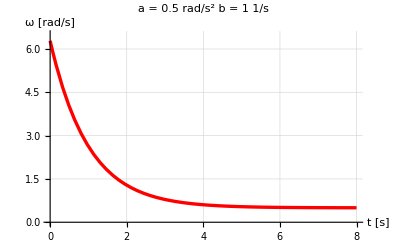

```mathematica
rys1=Plot[ω[t]/.A,{t,0,8},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotRange ->{{0,8},{0,6.5}},
GridLines->Automatic,
PlotLabel->StyleForm["      a = 0.5 rad/s^2      b = 1 1/s",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"t [s] ","ω [rad/s]"}]
```

```mathematica
a=1;       (* rad/s^2 *)
```

```mathematica
b=0.5;    (* 1/s *)
```

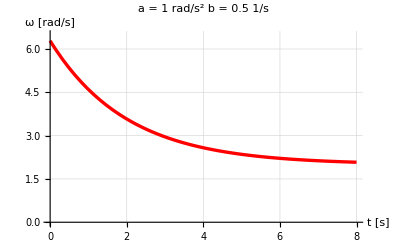

```mathematica
rys1=Plot[ω[t]/.A,{t,0,8},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotRange ->{{0,8},{0,6.5}},
GridLines->Automatic,
PlotLabel->StyleForm["      a = 1 rad/s^2      b = 0.5 1/s",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"t [s] ","ω [rad/s]"}]
```